```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/";
```

{{:0,:1,:2},{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

{{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

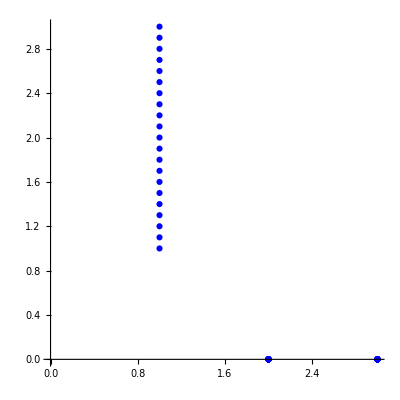

21

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabv=Table[Flatten[{{v[x],0,0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabv,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"v.csv",tabv]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/v.csv

```mathematica
(*write w from ODE to csv file*)
```

```mathematica
tabw=Table[{w[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"w.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/w.csv

```mathematica
(*write σ from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"sigma.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/sigma.csv

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{2.41199,3.,0,0},{2.44332,2.9,0,0},{2.43029,2.8,0,0},{2.37305,2.7,0,0},{2.27231,2.6,0,0},{2.12964,2.5,0,0},{1.94802,2.4,0,0},{1.7323,2.3,0,0},{1.48971,2.2,0,0},{1.22977,2.1,0,0},{0.963771,2.,0,0},{0.703671,1.9,0,0},{0.460778,1.8,0,0},{0.244653,1.7,0,0},{0.0625313,1.6,0,0},{-0.0806774,1.5,0,0},{-0.181995,1.4,0,0},{-0.239822,1.3,0,0},{-0.253443,1.2,0,0},{-0.222711,1.1,0,0},{-0.147969,1.,0,0}}

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/psi.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0.26715,3.,0,0},{0.0458243,2.9,0,0},{-0.175984,2.8,0,0},{-0.395839,2.7,0,0},{-0.610316,2.6,0,0},{-0.813906,2.5,0,0},{-0.998343,2.4,0,0},{-1.15278,2.3,0,0},{-1.26516,2.2,0,0},{-1.32475,2.1,0,0},{-1.32516,2.,0,0},{-1.26632,1.9,0,0},{-1.15459,1.8,0,0},{-1.00064,1.7,0,0},{-0.816524,1.6,0,0},{-0.61313,1.5,0,0},{-0.398756,1.4,0,0},{-0.178947,1.3,0,0},{0.0428521,1.2,0,0},{0.2642,1.1,0,0},{0.482413,1.,0,0}}

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/mu.csv

```mathematica
(*write X from ODE to csv file*)
```

```mathematica
tabX=Table[Flatten[{{X1[x],X2[x],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabX,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"X.csv",tabX]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/X.csv